```mathematica
Needs["SpectralBP`"]
```

# SpectralBP - Quasinormal Modes

In this notebook, we show how SpectralBP can be used in solving problems in gravity. We choose two very standard problems, the scalar and gravitational perturbations to the asymptotically flat Schwarzschild spacetime.

## Scalar perturbations

## Deriving a quasinormal mode equation

We begin with the Schwarzschild metric, defining the coordinates, the inverse metric, and the determinant of the metric along the way.

```mathematica
coordinates = {t,r,θ,ϕ};
metric = {{-(1-(2M)/r),0,0,0},{0,(1-(2M)/r)^-1,0,0},{0,0,r^2,0},{0,0,0,r^2(Sin[θ]^2)}};
metricinverse = Inverse[metric];
g = Det[metric];
```

A scalar perturbation Ψ[t,r,θ,ϕ] of a spacetime is a solution to the Klein-Gordon equation

```mathematica
eqn = 1/Sqrt[-g]∑_(μ=1)^4 ∑_(ν=1)^4 D[(metricinverse⟦μ,ν⟧Sqrt[-g] D[Ψ[t,r,θ,ϕ], coordinates⟦ν⟧]), coordinates⟦μ⟧];
```

We decompose the above equation into stationary spherical harmonic states.

```mathematica
Ψ[t_,r_,θ_,ϕ_]:= Exp[-ⅈ ω t] R[r]/r Y[θ,ϕ];
eqn2 = eqn//Simplify
```

(ⅇ^(-ⅈ t ω) ((2 M-r) r Y[θ,ϕ] (-2 M R'[r]+(2 M-r) r R''[r])+R[r] ((4 M^2-2 M r+r^4 ω^2) Y[θ,ϕ]+r (-2 M+r) (Csc[θ]^2 Y^(0,2)[θ,ϕ]+Cot[θ] Y^(1,0)[θ,ϕ]+Y^(2,0)[θ,ϕ]))))/(r^4 (-2 M+r))

Now, recall that the eigenvalue equation of Y[θ,ϕ] is given by Cot[θ] ∂_θ Y + (∂^2)_θ Y + Csc[θ]^2(∂^2)_ϕ Y= -l(l+1)Y. We can then factor out a Exp[-ⅈ ω t] Y[θ,ϕ] from the expression above.

```mathematica
eqn3 = (eqn2 /. Csc[θ]^2 Derivative[0,2][Y][θ,ϕ]+Cot[θ] Derivative[1,0][Y][θ,ϕ]+Derivative[2,0][Y][θ,ϕ] ->- l(l+1)Y[θ,ϕ])/(Exp[-ⅈ ω t] Y[θ,ϕ])//Simplify
```

((4 M^2+2 (-1+l+l^2) M r+r^2 (-l-l^2+r^2 ω^2)) R[r]+(2 M-r) r (-2 M R'[r]+(2 M-r) r R''[r]))/(r^4 (-2 M+r))

Finally, we nondimensionalize

```mathematica
eqn4 = eqn3 /. {R -> (R[#/(2M)]&),r -> 2 M r,ω-> ω/(2M)}//Simplify
```

((1+(-1+l+l^2) r-l (1+l) r^2+r^4 ω^2) R[r]+(-1+r) r (R'[r]+(-1+r) r R''[r]))/(8 M^3 (-1+r) r^4)

We factor out the overall 8 M^3 term, and collect all functions of r

```mathematica
eqn5 = eqn4*8 M^3//Simplify//Collect[#,_[r]]&
```

((1+(-1+l+l^2) r-l (1+l) r^2+r^4 ω^2) R[r])/((-1+r) r^4)+R'[r]/r^3+((-1+r) R''[r])/r^2

The canonical form is when the coefficient of the highest derivative is 1, so we multiply by r^2/(1-r)

```mathematica
eqnfinal  = eqn5*r^2/(r-1)//Simplify//Collect[#,_[r]]&
```

((1+(-1+l+l^2) r-l (1+l) r^2+r^4 ω^2) R[r])/((-1+r)^2 r^2)+R'[r]/((-1+r) r)+R''[r]

This is the relevant ordinary differential equation for calculating quasinormal modes of scalar perturbations to the asymptotically flat Schwarzschild spacetime

## Asymptotics

The asymptotics of this equation at both singular points at the black hole horizon (r = 1) and the cosmological horizon (r -> Infinity) are both well - known.

1. At r = 1, the solution entering the black hole horizon ~ 1, while the solution leaving the black hole horizon ~ r^-ⅈω
2. At r → Infinity, the solution entering the cosmological horizon ~ r^-ⅈωExp[-ⅈωr], while the solution leaving the cosmological horizon ~ r^ⅈωExp[ⅈωr].

A generic perturbation of the spacetime takes time to reach both these horizons, so by causality we wish to exclude solutions which enter both horizons. We accomplish this by noting that spectral methods converge exponentially only when approximating analytic functions. Thus, we would like to factor out some function that makes the solution which leaves both horizons analytic, and other solutions nonanalytic. One such factorization is the following :

```mathematica
R[r_] := r^(2ⅈ ω)(r-1)^(-ⅈ ω)Exp[ⅈ ω r] ϕ[r];
```

The function ϕ[r] diverges when describing solutions of the above equation that enters either horizon. Multiplying out common factors, we arrive at

```mathematica
eqnϕ = eqnfinal*Exp[-ⅈ ω r] (r-1)^(1 + ⅈ ω)r^(2-2ⅈ ω) // Simplify
```

-(1+l r+l^2 r-4 ⅈ ω-4 (1+r) ω^2) ϕ[r]+r ((1+2 ⅈ (-2+r^2) ω) ϕ'[r]+(-1+r) r ϕ''[r])

The domain of the solution in r is (1,∞). The domain must be compact to be able to use SpectralBP. We use the transformation r→ 1/u to accomplish this.

```mathematica
eqnϕ2 = u*(eqnϕ/.{ϕ->(ϕ2[1/#]&),r-> 1/u})//Simplify
```

-(l+l^2-4 ω^2-u (ⅈ+2 ω)^2) ϕ2[u]+(2 u+u^2 (-3+4 ⅈ ω)-2 ⅈ ω) ϕ2'[u]-(-1+u) u^2 ϕ2''[u]

This form can now be used in SpectralBP

## Eigenvalues

#### A note on the number of eigenvalues

Let us try calculating the QNMs using a basis of order 50, for l = 3

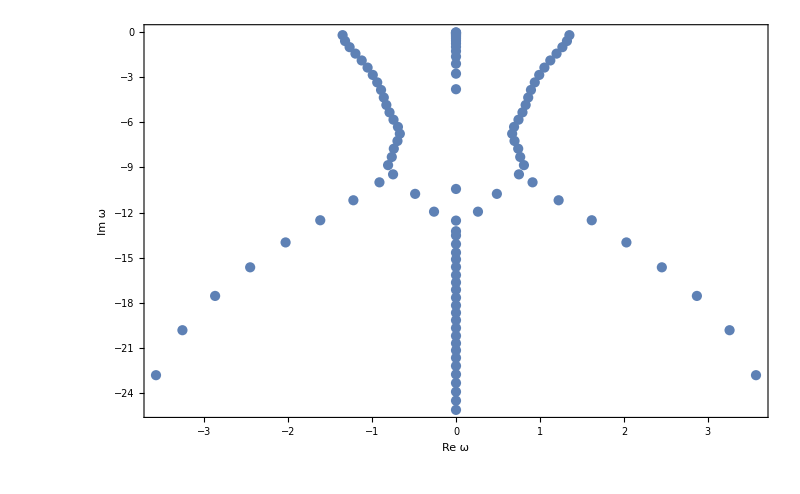

```mathematica
scalarmodes350 = GetModes[eqnϕ2/.l->3,{50,50}];
PrintFrequencies[scalarmodes350]
```

We have calculated the following number of eigenvalues

```mathematica
Length[scalarmodes350]
```

102

The command PrintTable pairs up complex eigenvalues that satisfy ω → -ω^* and ω → ω^*. Since PrintTable needs a pair of spectra as input (for the calculation of significant digits), we may instead reuse the same spectrum if we do not care about significant digits.

```mathematica
PrintTable[{scalarmodes350,scalarmodes350}]
```

Imaginary Eigenvalues |  | 
n | Re ω | Im ω
1 | 0.×10^-49 | -0.007608000143228369658787562738459333799382472511
2 | 0.×10^-49 | -0.0228844693600142038597929901669558407701454524867
3 | 0.×10^-49 | -0.0483820395158851117266367648998127061661920078337
4 | 0.×10^-49 | -0.0863956194151833290802685589980384559275140520707
5 | 0.×10^-49 | -0.1394157571583721064242081084163679914590541187477
6 | 0.×10^-50 | -0.2101944806127015393448400920961190957879193987149
7 | 0.×10^-52 | -0.3018834115443921091208466609600211688093948720023
8 | 0.×10^-53 | -0.4182636786415006063724991788284473429318520596738
9 | 0.×10^-55 | -0.5641139689374304663794113230942654733301151358929
10 | 0.×10^-54 | -0.7457998930583256431505082620131593221931044371453
11 | 0.×10^-55 | -0.9722417494722313193599772092449026482659352951859
12 | 0.×10^-54 | -1.2565988606757618582822045996120633085626368196375
13 | 0.×10^-55 | -1.6195118896051250900813028348109851677287995128708
14 | 0.×10^-53 | -2.0963566205814482489987357608685089211012822276495
15 | 0.×10^-51 | -2.757506461809904554702706309082445539550563948794
16 | 0.×10^-49 | -3.7925027740160010308248739233201222212878395141083
17 | 1.×10^-45 | -10.4329834730134324167792768290203797542161809440818
18 | -2.×10^-43 | -12.5398660429771290786418857555040372233814824896467
19 | -8.×10^-44 | -13.2455818826051830825602010627084462264382487432886
20 | 4.×10^-44 | -13.5296241284016213075184457901935468369067713692729
21 | 4.×10^-43 | -14.1045448526922647887654648786842663739611430455524
22 | 6.×10^-44 | -14.6696923289673986651528022574879119055466751656084
23 | -2.×10^-43 | -15.1186748322987749191209584279560168963535020851737
24 | -3.×10^-43 | -15.6263318828954612261808159291093049755370082756069
25 | 2.×10^-43 | -16.1654122017999544798244068691756281153003574975251
26 | 2.×10^-43 | -16.6586916189297229288179248986637476024571510013972
27 | -3.×10^-44 | -17.1461428709520072368154993821935764024857293289319
28 | -2.×10^-43 | -17.6674794954472173982470417825636204990523215223505
29 | 8.×10^-45 | -18.1852909558102610349492249046476937112615943902838
30 | 7.×10^-44 | -18.6752704566232319627473519618769835673543234984352
31 | -5.×10^-46 | -19.1685350840888198713227035575125641958099504584818
32 | -2.×10^-44 | -19.6882512563759583753907656789638571801173213959012
33 | 4.×10^-45 | -20.2116271505908731955938657160179133641329499327814
34 | 4.×10^-45 | -20.7061898729673216957152201254102220843637861029768
35 | -1.×10^-45 | -21.1758446069610092361217566390404793372043409522459
36 | -5.×10^-46 | -21.6739943060313519742617601944217300909088544277343
37 | 3.×10^-46 | -22.2135627498561098017718057678081811828412603651805
38 | -6.×10^-47 | -22.7764480423766661504120969303885909351375333965382
39 | 8.×10^-48 | -23.3510493673355986687006505112817458595340391709135
40 | -2.×10^-49 | -23.9335138908168505091789371947104594032375059758175
41 | 0.×10^-50 | -24.5257473246111155274134242641399162954732619158343
42 | 0.×10^-51 | -25.1401905946427227376246443695267561931594043849036
Complex Eigenvalues |  | 
n | Re ω | Im ω
1 | ± 3.5733144749737444831384405361173199388491087399387 | -22.8304097002453065046864418454549887693347902112845
2 | ± 3.2585999296766549427526678247166276839100473872456 | -19.8362266102158739862995885448636856759680146360868
3 | ± 2.8692257806227212270369640500309389001406337229945 | -17.5540915951811945262526244777353774847470993741475
4 | ± 2.4517600119394169517736524492087449621629477677394 | -15.6496624751646930614573204627869396195021212834792
5 | ± 2.0297557845601612754444063318866181871259630146304 | -13.9926630307698803482302828711434345666372556324958
6 | ± 1.6168593446177400452565355508678232408019495448127 | -12.5166311227915377948361774738988298296007683946316
7 | ± 1.3507324650732410704378681044741689211729443731702 | -0.1929992554680191676833017531511609186144685544502
8 | ± 1.3213429959119264316004217626251142625207264225019 | -0.5845695702768245801282870758185980199329401416042
9 | ± 1.2672516153856922141283348208545392379098561592887 | -0.9920164608060652859377497597491112740127923106706
10 | ± 1.2224153253587972213016162436425372711824954134497 | -11.1858732955077274103774803491997272800849284199261
11 | ± 1.1975465065352908251329219868161129312818056212869 | -1.422442413856091579247255051377733418018417703556
12 | ± 1.1232545905219613656174394452459929266869015865123 | -1.8771857908488094929612896778721721697003280224893
13 | ± 1.0530964841032608483897501447722020135931745279763 | -2.3520650212122724969561790993944550144132411001039
14 | ± 0.9913159988290381639213626228022581146111709718963 | -2.8408319297327767047261380179664252017714642034267
15 | ± 0.9382312066501259139916591864992547053853525465699 | -3.3375480562348197055295711302911417372785267338986
16 | ± 0.9117830774074675327869179163505890214987543509171 | -9.9915754493240975145364825822694602702163368572554
17 | ± 0.8927734087497257883873620847961106868319247842502 | -3.8414072114248840623627533577719797270652146765313
18 | ± 0.8600305493191209869355584795157983840551936529973 | -4.3458494951834336563671899296135450947357644467207
19 | ± 0.8296073461223636400104333018558729615335216861007 | -4.8415222614295248896791956649458186505805730857905
20 | ± 0.809044464657200971326745366372299697011870021949 | -8.8470445994020870642566931057817390965004236733797
21 | ± 0.7917554390323776759100554570536455724709910441789 | -5.3332058833981859341512859289114228522478939115541
22 | ± 0.7648884244168045637431916396631334779266344796908 | -8.3042678697278475159658615721639868185287719076498
23 | ± 0.7495850548310681947304691259878664728295832630359 | -9.4603958399974783447433314566364101809845313181034
24 | ± 0.7442595601649967478762607230990989232013454311725 | -5.8229891345499528195346811419546047590022579580066
25 | ± 0.7407908814487279380294523983177384686853317935353 | -7.7529725336740295652297807359405280525843078399743
26 | ± 0.6971976592875527200889707446847839626983355574005 | -7.2371626826428577807990436769188838863215029685217
27 | ± 0.6916091504031354839238035940181171559082723059507 | -6.301175640515026717193198275465419193823556977972
28 | ± 0.668982280460628669159300004077434442356981043652 | -6.7566031431384252699088498553065428944976377544721
29 | ± 0.4867849420200800035539188197456693894407816920185 | -10.7592966401806972553006225444986775794930811837131
30 | ± 0.2616685599802599952276641820725091204436481058008 | -11.9447947483161674055130096720503687351102072791374

This is because we started with a quadratic eigenvalue problem using a basis of order 50 (or a total of 51 basis functions). Many of these modes a are spurious, so we use the CompareModes function to filter out some of these eigenvalues.

#### A note on CompareModes - Spurious eigenvalues

Let us now calculate the QNMs using a basis of order 80 this time.

```mathematica
scalarmodes380 = GetModes[eqnϕ2/.l->3,{80,80}];
scalarmodes35080 = CompareModes[scalarmodes380,scalarmodes350];
PrintTable[scalarmodes35080]
```

Imaginary Eigenvalues |  | 
n | Re ω | Im ω
1 | 0.×10^-65 | -18.67
2 | 0.×10^-65 | -20.7
3 | 0.×10^-64 | -22.21
Complex Eigenvalues |  | 
n | Re ω | Im ω
1 | ± 1.350732465073241071 | -0.192999255468019168
2 | ± 1.32134299591192 | -0.58456957027682
3 | ± 1.26725161539 | -0.992016460806
4 | ± 1.19754651 | -1.42244241
5 | ± 1.1232546 | -1.877186
6 | ± 1.0531 | -2.35207
7 | ± 0.9913 | -2.8408
8 | ± 0.938 | -3.338

There are no known purely imaginary quasinormal modes for the scalar case. We are pretty sure that these modes are spurious. There are two ways to filter out these spurious modes: (1) calculate using another order of basis polynomials or (2) use the CompareEigenfunctions command.

The CompareModes function can compare more than two spectra. The proper syntax is to feed the function with a list of spectra. The PrintTable function still only accepts two spectra.

```mathematica
scalarmodes3100 = GetModes[eqnϕ2/.l->3,{100,100}];
scalarmodes35080100 = CompareModes[{scalarmodes3100,scalarmodes380,scalarmodes350}];
PrintTable[scalarmodes35080100⟦1;;2⟧]
```

Complex Eigenvalues |  | 
n | Re ω | Im ω
1 | ± 1.3507324650732410706405159 | -0.19299925546801916775379297
2 | ± 1.32134299591192494964 | -0.58456957027682377316
3 | ± 1.26725161538864733 | -0.9920164608062535
4 | ± 1.1975465055999 | -1.422442414743
5 | ± 1.1232545798 | -1.8771856473
6 | ± 1.0530996 | -2.35206873
7 | ± 0.991268 | -2.84079
8 | ± 0.93841 | -3.33793

On the other hand, we may use CompareEigenfunctions[eqn, spectra, Nmaxes]. Here, eqn and spectra is the equation and the spectra to be compared respectively. One must specify the correct boundary conditions from which spectra was calculated. Nmaxes is a list of grid sizes, to which one checks if the numbers in spectra are approximate eigenvalues of those grid sizes. If they are not, the corresponding eigenfunctions for different grid sizes should not converge.

Let us isolate the purely imaginary frequencies:

```mathematica
testscalarmodes = Table[Select[scalarmodes35080⟦k⟧,Abs[Re[#]]<10^-20&],{k,2}];
```

```mathematica
scalarmodes35080b = CompareEigenfunctions[eqnϕ2/.l->3,testscalarmodes ,{80,50}]
```

{}

None of the imaginary eigenvalues have consistent eigenfunctions.

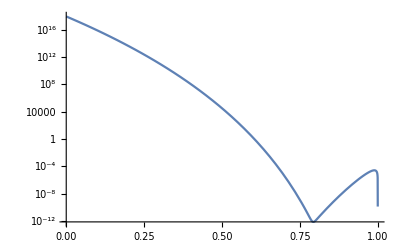

```mathematica
scalareigen1 = GetEigenfunctions[eqnϕ2/.l->3,{testscalarmodes⟦1,1⟧},80,u];
scalareigen2 = GetEigenfunctions[eqnϕ2/.l->3,{testscalarmodes⟦2,1⟧},50,u];
Quiet[LogPlot[Abs[scalareigen1-scalareigen2],{u,0,1},WorkingPrecision->80]]
```

Compare this to one of complex eigenvalues

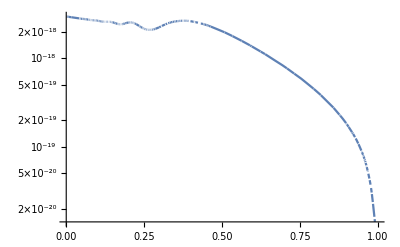

```mathematica
scalareigen3 = GetEigenfunctions[eqnϕ2/.l->3,{scalarmodes35080⟦1,1⟧},80,u];
scalareigen4 = GetEigenfunctions[eqnϕ2/.l->3,{scalarmodes35080⟦2,1⟧},50,u];
Quiet[LogPlot[Abs[scalareigen3-scalareigen4],{u,0,1},WorkingPrecision->80]]
```

Thus we may filter out the purely imaginary modes

```mathematica
scalarmodes38050c = Table[Select[scalarmodes35080⟦k⟧,Abs[Re[#]]>10^-20&],{k,2}];
PrintTable[scalarmodes38050c]
```

Complex Eigenvalues |  | 
n | Re ω | Im ω
1 | ± 1.350732465073241071 | -0.192999255468019168
2 | ± 1.32134299591192 | -0.58456957027682
3 | ± 1.26725161539 | -0.992016460806
4 | ± 1.19754651 | -1.42244241
5 | ± 1.1232546 | -1.877186
6 | ± 1.0531 | -2.35207
7 | ± 0.9913 | -2.8408
8 | ± 0.938 | -3.338

One may check all eigenvalues, but this may take a considerable amount of time when the grid sizes are large

```mathematica
scalarmodes38050d = CompareEigenfunctions[eqnϕ2/.l->3,scalarmodes35080 ,{80,50}];//Timing
PrintTable[scalarmodes38050d]
```

{36.7969,Null}

Complex Eigenvalues |  | 
n | Re ω | Im ω
1 | ± 1.35073246507324107 | -0.192999255468019168
2 | ± 1.32134299591193 | -0.58456957027682
3 | ± 1.26725161539 | -0.992016460806
4 | ± 1.19754651 | -1.42244241
5 | ± 1.1232546 | -1.877186
6 | ± 1.0531 | -2.35207
7 | ± 0.9913 | -2.8408
8 | ± 0.938 | -3.338

#### A note on complex and real equations - Speeding up calculations

Notice that eqnϕ2 becomes purely real with the replacement ω → ⅈ λ. The resulting spectral matrices are real valued, which Mathematica handles better than a general complex valued matrix.

```mathematica
eqnϕ3 = (eqnϕ2 /.ω->ⅈ λ )//Collect[#,_[u],Simplify]&;
GetModes[eqnϕ3/.l->3,{50,50}];//Timing
GetModes[eqnϕ2/.l->3,{50,50}];//Timing
```

{3.6875,Null}

{11.5781,Null}

## Eigenfunctions

Let us calculate the first 3 eigenfunctions corresponding to the eigenvalues with positive real part

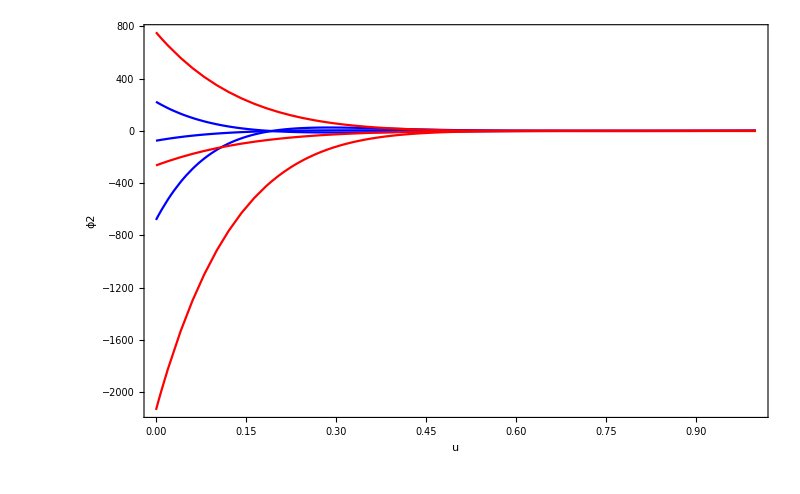

```mathematica
PrintEigenfunctions[eqnϕ2/.l->3,Reverse[Select[scalarmodes38050c⟦1⟧,Re[#]<0&]]⟦1;;3⟧,80]
```

We may retrieve the eigenfunctions, and return to our original coordinate system:

```mathematica
scalareigens = GetEigenfunctions[eqnϕ2/.l->3,Reverse[Select[scalarmodes38050c⟦1⟧,Re[#]>0&]]⟦1;;3⟧,80,u]/.u->1/r;
```

We may then rescale in the nonanalytic parts we have rescaled out

```mathematica
scalareigens = (r^(2ⅈ ω)(r-1)^(-ⅈ ω)Exp[ⅈ ω r]/.ω->Reverse[Select[scalarmodes38050c⟦1⟧,Re[#]>0&]]⟦1;;3⟧)*scalareigens;
```

Resulting in the following real and imaginary parts of the complete QNM eigenfunctions

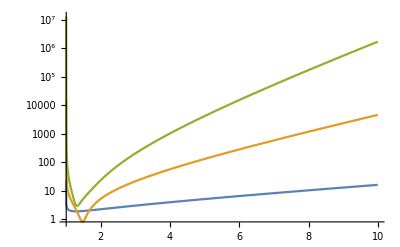

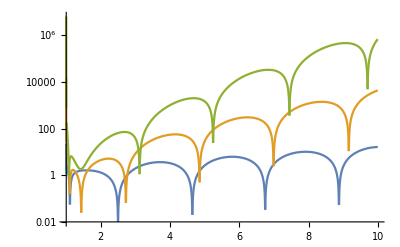

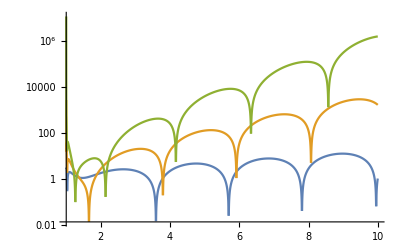

```mathematica
Quiet[LogPlot[Evaluate@Abs[scalareigens],{r,1,10},WorkingPrecision->80]]
Quiet[LogPlot[Evaluate@Abs[Re[scalareigens]],{r,1,10},WorkingPrecision->80]]
Quiet[LogPlot[Evaluate@Abs[Im[scalareigens]],{r,1,10},WorkingPrecision->80]]
```

```mathematica
W
```

## Gravitational perturbations

## Regge-Wheeler Equation

We begin with the Regge-Wheeler Equation

```mathematica
eqn = R''[r] + 1/(r(r-1))R'[r] + (ω^2 r^4-l(l+1)r^2+(l(l+1)+s^2-1)r  + 1 - s^2)/(r^2(r-1)^2)R[r];
```

It has the following asymptotic solution at the cosmological horizon r = ∞. A solution entering the cosmological horizon that goes like ~r^-ⅈω Exp[-ⅈωr], and a solution leaving the cosmological horizon that goes like ~r^ⅈωExp[ⅈωr]. The causal solution is the latter one. 

On the other hand, it has a regular singularity at the black hole horizon. Using the Frobenius method, we solve for the asymptotic expansion at r = 1

```mathematica
p[r_]:= 1/r;q[r_]:=(ω^2 r^4-l(l+1)r^2+(l(l+1)+s^2-1)r  + 1 - s^2)/r^2;
Solve[x(x-1) + p[1]x  + q[1] ==0,x]
```

{{x→-ⅈ ω},{x→ⅈ ω}}

The solution entering the black hole horizon goes like ~ (r-1)^ⅈω while the solution leaving the black hole horizon goes like ~ (r-1)^-ⅈω. The causal solution is the latter. Thus, we may factor out a (r^(2ⅈω)(r-1))^-ⅈω Exp[ⅈωr] so that the causal solution is analytic (goes like ~1 at both horizons) while the acausal solutions diverge (~r^(-2ⅈω)Exp[-2ⅈωr] at the cosmological horizon, ~ (r-1)^(2ⅈω) at the black hole horizon)

```mathematica
R[r_] := r^(2ⅈ ω)(r-1)^(-ⅈ ω)Exp[ⅈ ω r] ϕ[r];
eqnϕ = eqn*r^(2-2ⅈ ω)(r-1)^(1+ⅈ ω)Exp[-ⅈ ω r]//Collect[#,_[r],Simplify]&
```

(-1-l r-l^2 r+s^2+4 ⅈ ω+4 ω^2+4 r ω^2) ϕ[r]+(r-4 ⅈ r ω+2 ⅈ r^3 ω) ϕ'[r]+(-1+r) r^2 ϕ''[r]

We now compactify with the change of variables r → 1/u.

```mathematica
eqnϕ2 = u*(eqnϕ/.{ϕ->(ϕ2[1/#]&),r-> 1/u,ω->ⅈ λ})//Collect[#,_[u],Simplify]&
```

(-l-l^2-4 λ^2+u (s^2-(1+2 λ)^2)) ϕ2[u]+(2 u+2 λ-u^2 (3+4 λ)) ϕ2'[u]-(-1+u) u^2 ϕ2''[u]

```mathematica
eqnϕ3= u*(eqnϕ/.{ϕ->(ϕ2[1/#]&),r-> 1/u})//Collect[#,_[u],Simplify]&
```

(-l-l^2+4 ω^2+u (s^2+(ⅈ+2 ω)^2)) ϕ2[u]+(2 u+u^2 (-3+4 ⅈ ω)-2 ⅈ ω) ϕ2'[u]-(-1+u) u^2 ϕ2''[u]

## Special Algebraic Modes

Gravitational perturbations are known to have special algebraic modes, which are purely imaginary QNM frequencies. We show that the function 

We calculate QNMs for gravitational perturbations for l = 2, and compare the two calculations. We calculate using the purely real ODE, and return the ⅈ after the fact.

```mathematica
GWmodes2400= GetModes[eqnϕ2/.{l->2,s->2},{400,200}];//Timing
GWmodes2350= GetModes[eqnϕ2/.{l->2,s->2},{350,175}];//Timing
```

{1825.38,Null}

{1143.66,Null}

Imaginary Eigenvalues |  | 
n | Re ω | Im ω
1 | 0 | -4.
2 | 0 | -140.7
Complex Eigenvalues |  | 
n | Re ω | Im ω
1 | ± 0.7473433688360836715869840059540965403707760942006789138 | -0.1779246313778713965609218543690451563939684474003217457
2 | ± 0.69342199375832687943535071946667156077 | -0.547829750582469634699120444276358549496
3 | ± 0.60210690922473278760400722 | -0.95655396644614361996836566
4 | ± 0.50300992437118118 | -1.4102964048669907372
5 | ± 0.415029159626 | -1.8936897817327
6 | ± 0.33859881 | -2.39121611
7 | ± 0.2665046 | -2.895821
8 | ± 0.1856 | -3.4077

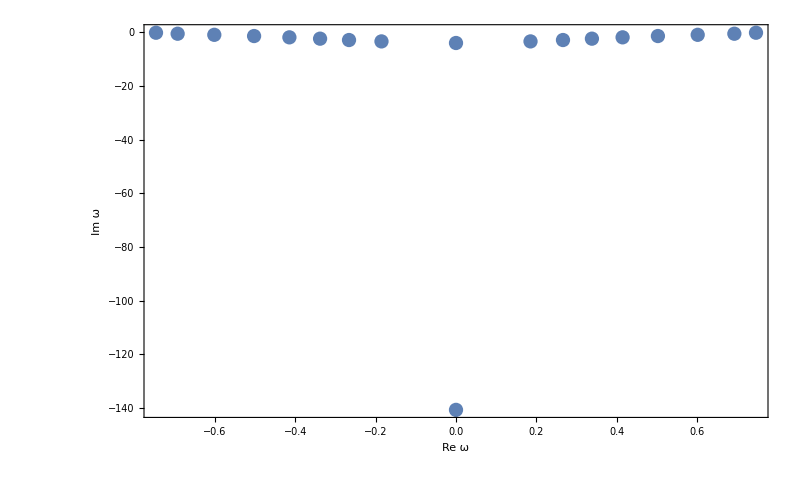

```mathematica
GWmodes2400350 = CompareModes[GWmodes2400,GWmodes2350,Cutoff->4];
PrintTable[ⅈ*GWmodes2400350]
PrintFrequencies[ⅈ*GWmodes2400350⟦1⟧]
```

We wish to show that the special algebraic mode is the only nonspurious purely imaginary mode.

```mathematica
GWmodes2test = Table[Select[GWmodes2400350⟦k⟧,Abs[Im[#]]<10^-20&],{k,2}];
GWmodes2testb = CompareEigenfunctions[eqnϕ2/.{s->2,l->2},GWmodes2test,{400,350}]
```

{{-4.000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000002616721916902399399},{-3.9999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999999975173785519}}

As one can see, only the special algebraic mode has survived the CompareEigenfunctions filter. We may now remove the offending eigenvalues from our data

```mathematica
badeigenvalues = Table[Complement[GWmodes2test⟦k⟧,Reverse[GWmodes2testb]⟦k⟧],{k,2}]
```

{{-140.65891570937575825579508258223108079106947306923981704412648652359606422073481460865774947719478768672126741226541412251241271898122563719466121664695916194904937403400402234379296984039152040674375},{-140.6675607600849496079767245216110753357099484575021691684362654743979415759083473843443410187852522765337928448780070449170383363109300167826639878613127082930270790980151057}}

Imaginary Eigenvalues |  | 
n | Re ω | Im ω
1 | 0 | -4.
Complex Eigenvalues |  | 
n | Re ω | Im ω
1 | ± 0.7473433688360836715869840059540965403707760942006789138 | -0.1779246313778713965609218543690451563939684474003217457
2 | ± 0.69342199375832687943535071946667156077 | -0.547829750582469634699120444276358549496
3 | ± 0.60210690922473278760400722 | -0.95655396644614361996836566
4 | ± 0.50300992437118118 | -1.4102964048669907372
5 | ± 0.415029159626 | -1.8936897817327
6 | ± 0.33859881 | -2.39121611
7 | ± 0.2665046 | -2.895821
8 | ± 0.1856 | -3.4077

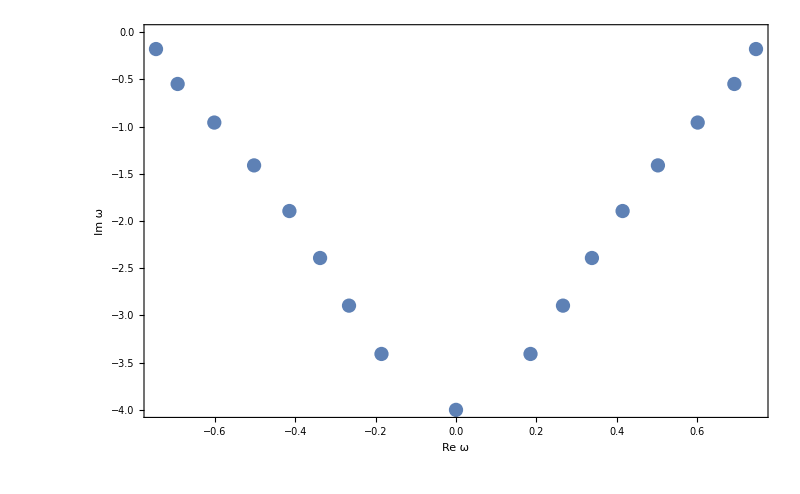

```mathematica
GWmodes2testc = Table[Complement[GWmodes2400350⟦k⟧,badeigenvalues⟦k⟧],{k,2}];
PrintTable[ⅈ*GWmodes2testc]
PrintFrequencies[ⅈ*GWmodes2testc⟦1⟧]
```